## Functions

```mathematica
θ[x_,thresh_]:=If[x<thresh,0,1];
πD[b_,num_,thresh_]:=b θ[num,thresh]+1;
πC[b_,c_,num_,thresh_]:=πD[b,num,thresh]-c/num  θ[num,thresh]-c/thresh (1-θ[num,thresh]);
πintraD[d_,b_,c_,num_,ω_]:=b/d∑_(i=0)^(num-1) ω^i;
πintraC[d_,b_,c_,num_,ω_]:=πintraD[d,b,c,num,ω]-c;
fD[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=p(∑_(k=0)^(d-1) (Binomial[d-1,k] x^k (1-x)^(d-1-k) πD[b,k,thresh]))+(1-p)(∑_(k=0)^(d-1) (Binomial[d-1,k] y^k (1-y)^(d-1-k) πintraD[dintra,bintra,cintra,k,ω]));
fC[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=p(∑_(k=0)^(d-1) (Binomial[d-1,k] x^k (1-x)^(d-1-k) πC[b,c,k+1,thresh]))+(1-p)(∑_(k=0)^(d-1) (Binomial[d-1,k] y^k (1-y)^(d-1-k) πintraC[dintra,bintra,cintra,k+1,ω]));
fbar1[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=x fC[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p]+(1-x)fD[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p];
fbar2[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=y fC[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p]+(1-y)fD[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p];
xdot[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,m_,ω_,p_]:=m x (1-x) (fC[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p] - fD[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p]);
ydot[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,n_,ω_,p_]:=n y (1-y)(fC[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p] - fD[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p]);
```

```mathematica
checkinternal[point_]:=If[point⟦1⟧>0&&point⟦1⟧<1&&point⟦2⟧>0&&point⟦2⟧<1,1,0];
```

```mathematica
plotrange={{-0.02,1.02},{-0.02,1.02}};
```

## Parameters

```mathematica
ClearAll[n,ω,ω1,ω2,r1,r2,d,p]
```

```mathematica
gamea={3,3/4};
gameb={1,3/4};
gamec={1,4/3};
gamed={3,4/3};

d1=5;
d2=5;
d1intra=5;
d2intra=5;
thresh1=1;
thresh2=1;
b=2;
c=1;
bintraforsp1=10;
cintraforsp1=gameb⟦1⟧;
ωforsp1=gameb⟦2⟧//N;

bintraforsp2=10;
cintraforsp2=gameb⟦1⟧;
ωforsp2=gameb⟦2⟧//N;

m=1/8//N;
n=1;
lim=100;
```

## Functions for fluctuations

```mathematica
a=10;
diff=0;
num[t_]:=(Sin[a t-diff ]+1)/2;(*If[Sin[a t]>0,1/(1+A Sin[a t]),1-A Sin[a t]]*)
mean=Mean[Table[num[t],{t,0,20 π,0.0001}]];
(*geomean=GeometricMean[Table[num[t],{t,0,20 π,0.0001}]]*)
```

0.5

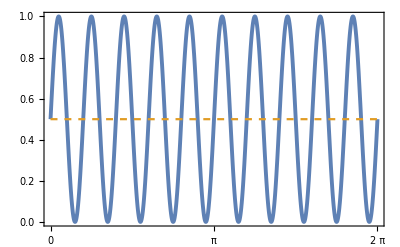

```mathematica
Plot[{num[t],mean},{t,0,2 π},PlotStyle->{{Thickness[0.007]},{Thickness[0.004],Dashed},{Thickness[0.004]}},PlotRange->{Automatic,Automatic},Frame->True,FrameStyle->Thickness[0.0025],FrameTicks->{{Automatic,Automatic},{{0,Pi,2Pi,15Pi,20Pi},None}},ImagePadding->20]
```

## Analysis

```mathematica
plotlis={};
plotdata={};
tlim=100;
For[i=0.1,i≤0.9,i=i+0.1,
For[j=0.1,j≤0.9,j=j+0.1,
sinlistcheck={};
s=Quiet[NDSolve[{
x'[t]== m x[t] (fC[d1,d1intra,y[t],x[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,num[t]] - fbar1[d1,d1intra,x[t],y[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,num[t]]),y'[t]==n y[t] (fC[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,num[t]] - fbar2[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,num[t]]),
x[0]==i,y[0]==j},{x,y},{t,0,tlim},MaxStepSize->0.005]];
tabsin=Table[{Evaluate[x[t]/.s]⟦1⟧,Evaluate[y[t]/.s]⟦1⟧},{t,0,tlim}];
AppendTo[plotdata,tabsin];
]
]
```

```mathematica
res[p_,q_,lim_]:=Quiet[NDSolve[{x'[t]== m x[t] (fC[d1,d1intra,y[t],x[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,num[t]] - fbar1[d1,d1intra,x[t],y[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,num[t]]),y'[t]==n y[t] (fC[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,num[t]] - fbar2[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,num[t]]),x[0]==p,y[0]==q},{x,y},{t,lim}]];
liseval[t_,rep_]:=Evaluate[{x[t],y[t]}/.rep];
```

ReplaceAll::reps: {rep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Clear[blue,red,black];
blue={};
red={};
black={};
For[u=0.0,u≤1.0,u=u+0.01,For[v=0.0,v≤1.0,v=v+0.01,
If[
liseval[lim,res[u,v,lim]]⟦1⟧⟦1⟧>0.9999&&liseval[lim,res[u,v,lim]]⟦1⟧⟦2⟧<0.001,AppendTo[red,{u,v}],If[liseval[lim,res[u,v,lim]]⟦1⟧⟦1⟧<0.001&&liseval[lim,res[u,v,lim]]⟦1⟧⟦2⟧>0.9999,AppendTo[blue,{u,v}],AppendTo[black,{u,v}]]];
]]
```

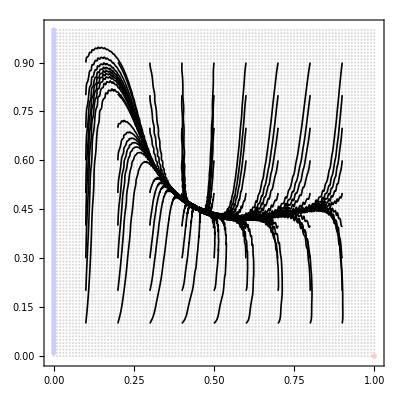

```mathematica
g1=ListPlot[{blue,red,black},PlotStyle->{Lighter[Blue,0.8],Lighter[Red,0.4],Lighter[Gray,0.7]},AspectRatio->1,Frame->True,PlotRange->{{-0.01,1.01},{-0.01,1.01}}];

plotcolors={};
For[i=1,i≤Length[plotdata],i++,
If[Last[plotdata⟦i⟧]⟦1⟧≥0.99&&Last[plotdata⟦i⟧]⟦2⟧≤0.01,AppendTo[plotcolors,{Darker[Red],Thickness[0.003]}],
If[Last[plotdata⟦i⟧]⟦2⟧≥0.99&&Last[plotdata⟦i⟧]⟦1⟧≤0.01,
AppendTo[plotcolors,{Darker[Blue],Thickness[0.003]}],AppendTo[plotcolors,{Black,Thickness[0.003]}]
]
];
]
Show[g1,ListPlot[{blue,red},PlotStyle->{Lighter[Blue,0.8],Lighter[Red,0.8]},AspectRatio->1,Frame->True,PlotRange->plotrange],ListPlot[plotdata,Joined->True,InterpolationOrder->2,AspectRatio->1,PlotRange->plotrange,PlotStyle->plotcolors,Frame->True],
Frame->True,FrameStyle->Thickness[0.0025],ImagePadding->17]
```